-Graphics3D-

-Graphics3D-

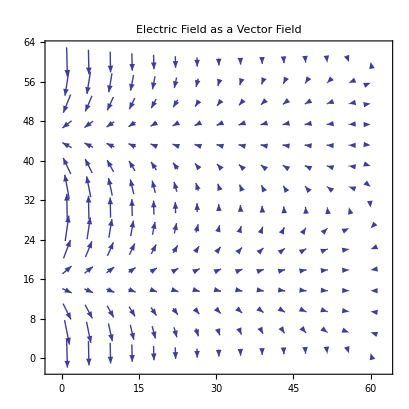

```mathematica
list  = Flatten[
Table[
{{i stepSize,j stepSize},potential[[j + (MM-1)(i-1)]]},
{i,1,NN},
{j,1,MM-1}
],1
];
edge = 
Table[
{{i stepSize,MM  stepSize},potential[[1 + (MM-1)(i-1)]]},
{i,1,NN}
];

list = Join[list, edge];
interp=Interpolation[list];

Plot3D[interp[x,y],{x,stepSize,NN stepSize},{y,stepSize, MM stepSize},PlotLabel->"Voltage"]

funcinterp=Function[{a,b},interp[a,b]];
funcx=Function[{a,b},Evaluate[D[funcinterp[a,b],a]]];
funcy=Function[{a,b},Evaluate[D[funcinterp[a,b],b]]];
Plot3D[√(funcx[a,b]^2+funcy[a,b]^2),{a,stepSize,NN stepSize},{b,stepSize,MM stepSize},PlotLabel->"Magnitude of Electric Field"]

ListVectorPlot[
Table[{funcx[a,b],funcy[a,b]},
{a,stepSize,NN stepSize},
{b,stepSize,MM stepSize}
]
,PlotLabel->"Electric Field as a Vector Field"]
```